## CONFORMAL DATA BY DIAGONALIZING A QUANTUM SPIN CHAIN HAMILTONIAN

We use the MERA package to also solve some excersizes using ncon, as an alternative solution.

```mathematica
SetDirectory[NotebookDirectory[]];
<<MERA.m
```

### Hamiltonian

```mathematica
hamiltonian[n_]:=Module[{listZ,listXX},
Sum[
listZ=Table[IdentityMatrix[d],{i-1}]~Join~{-PauliMatrix[3]}~Join~Table[IdentityMatrix[d],{n-i}];
listXX=Table[IdentityMatrix[d],{i-1}]~Join~{-PauliMatrix[1],PauliMatrix[1]}~Join~Table[IdentityMatrix[d],{n-i-1}];
If[i==n,listXX={listXX⟦-1⟧}~Join~listXX⟦2;;-2⟧];
listXX⟦0⟧=Sequence;
listZ⟦0⟧=Sequence;
KroneckerProduct[listZ]+KroneckerProduct[listXX],{i,n}]]
```

Check it is hermitian (for n=2..12):

```mathematica
Timing[(0==(hamiltonian[#]-hamiltonian[#]†//Abs//Max))&/@Range[2,12]]
```

{0.012993,{0==Abs[-(KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d]])^*+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d]]],0==Abs[-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]^†-KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]^†-KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]^†-KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],{{0,-1},{-1,0}}]^†+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]+KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],{{0,-1},{-1,0}}]],0==Abs[-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]^†-KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]^†-KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]^†+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]],0==Abs[-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]^†+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]],0==Abs[-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]^†+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]],0==Abs[-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]^†+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]],0==Abs[-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]^†+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]],0==Abs[-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]^†+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]],0==Abs[-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]^†+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]],0==Abs[-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]^†+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]],0==Abs[-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]^†-KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]^†+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}}]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[IdentityMatrix[d],{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{-1,0},{0,1}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,-1},{-1,0}},{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d]]+KroneckerProduct[{{0,1},{1,0}},IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],IdentityMatrix[d],{{0,-1},{-1,0}}]]}}

In this excersize we also do the same operations using ncon (see excersizes on MERA). (also to be used later with different coupling+field)

```mathematica
isinginteraction=ncon[{-PauliMatrix[1],PauliMatrix[1]},{{-1,-3},{-2,-4}}];
isingfield=-PauliMatrix[3];
Options[hamiltonianNcon]={periodic->True,interaction-> isinginteraction,field->isingfield };
hamiltonianNcon[length_,OptionsPattern[]]:=Module[{twositeH,tensors,legs},
d=Dimensions[OptionValue[field]]⟦1⟧;
If[Dimensions[OptionValue[field]]=!= {d,d}||Dimensions[OptionValue[interaction]]=!= {d,d,d,d},Print["invalid input"],
twositeH=ncon[{OptionValue[field],IdentityMatrix[d]},{{-1,-3},{-2,-4}}]+OptionValue[interaction];
Sum[
tensors=Table[IdentityMatrix[d],{i-1}]~Join~{If[i==length-1,ncon[{IdentityMatrix[d],OptionValue[field]},{{-1,-3},{-2,-4}}],0]+twositeH}~Join~Table[IdentityMatrix[d],{length-1-i}];
legs=Table[{-j,-length-j},{j,i-1}]~Join~{{-i,-i-1,-i-length,-i-length-1}}~Join~Table[{-j,-length-j},{j,i+2,length}];
ncon[tensors,legs],{i,length-1}]+
If[OptionValue[periodic],ncon[Table[IdentityMatrix[d],{length-2}]~Join~{OptionValue[interaction]},Table[{-j,-length-j},{j,2,length-1}]~Join~{{-length,-1,-2 length,-length-1}}],0]
]]
hamiltonianNconM[length_,opts___]:=ArrayReshape[hamiltonianNcon[length,opts],{d^length,d^length}]
hamiltonianNconME[length_,opts___]:=(Eigenvalues[hamiltonianNconM[length,opts]//N]//Chop//Union)⟦1;;-1⟧;
```

```mathematica
Timing[(0==(hamiltonianNconM[#]-hamiltonianNconM[#]†//Abs//Max))&/@Range[2,12]]
```

{11.54688,{True,True,True,True,True,True,True,True,True,True,True}}

```mathematica
Timing[(0==(hamiltonianNconM[#]-hamiltonian[#]//Abs//Max))&/@Range[2,10]]
```

{0.6875,{True,True,True,True,True,True,True,True,True}}

### Translation operator

```mathematica
d=2;
translation[n_]:=Module[{binaryI,binaryJ},
Table[
binaryI=IntegerDigits[i-1,2,n];
binaryJ=IntegerDigits[j-1,2,n];
If[binaryJ⟦2;;⟧~Join~{binaryJ⟦1⟧}==binaryI,1,0]
,{i,2^n},{j,2^n}]]
```

Check that indeed the Hamiltonian is translationally invariant :

```mathematica
Timing[(0==(translation[#].hamiltonian[#].translation[#]†-hamiltonian[#]//Abs//Max))&/@Range[2,8]]
```

{1.0625,{True,True,True,True,True,True,True}}

Here the power of ncon is more obvious :

```mathematica
translationncon[n_]:=ncon[Table[IdentityMatrix[2],{n}],Table[{-j,If[j<n,-j-n-1,-n-1]},{j,n}]]
translationnconM[n_]:=ArrayReshape[translationncon[n],{#,#}&[2^n]]
```

```mathematica
Timing[(0==(translationnconM[#].hamiltonian[#].translationnconM[#]†-hamiltonian[#]//Abs//Max))&/@Range[2,10]]
```

{0.95313,{True,True,True,True,True,True,True,True,True}}

### Diagonalize H

The eigensystem of  H, sorted, and keeping only the first 12 states

```mathematica
energystates[n_]:=Transpose[Sort[Thread[Eigensystem[hamiltonian[n]//N]]]⟦;;12⟧]
momentumstates[n_]:=Transpose[Sort[Thread[Eigensystem[translationnconM[n]//N]]]]
```

Example for n = 6 :

```mathematica
Dimensions/@energystates[6]
energystates[6]⟦1⟧
```

{{12},{12,64}}

{-7.72741,-7.4641,-5.65685,-5.4641,-5.4641,-4.,-4.,-3.8637,-3.8637,-3.8637,-3.8637,-3.4641}

### Find momenta

Here unfortunately we need a bit of a trick. We’re looking for simultaneous eigenvectors of H and T, which Mathematica does not provide a method for. You will find that just finding the eigenvectors for H and T does not suffice when the eigenvalues are degenerate. The trick is to compute the eigenvectors of a linear combination of H and T, which usually avoids the problem with the degeneracy. We have to re-extract the corresponding eigenvalues of the eigenvectors found, where we had to deal with dividing by zero for some elements of the vector (filtered out by discarding Indeterminate entries).

```mathematica
energystates2[n_]:=Module[{(*newvectors,newvalues,*)hamil=hamiltonian[n]},
newvectors=Eigensystem[hamil+translationnconM[n]3/2//N]⟦2⟧;
Quiet[newvalues=(vector↦(Mean[Select[Chop[hamil.vector]/Chop[vector],#=!=Indeterminate&]]))/@newvectors];
Transpose[Sort[Thread[{newvalues,newvectors}]]⟦;;12⟧]
]
```

Indeed the eigenvalues are the same, and also the non-denegerate eigenvectors. After that, however, the eigenvectors change.

```mathematica
energystates2[4]⟦1⟧//Chop
Abs[energystates2[4]]-Abs[energystates[4]]//Chop
```

{-5.22625,-4.82843,-2.16478,-2.,-2.,-0.828427,0,0,0,0,0.828427,2.}

{{0,0,0,0,0,0,0,0,0,0,0,0},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.275989,-0.170685,0,0.275989,0,0,0,-0.170685,0,0,0,0,0,0,0},{0,-0.170685,0.275989,0,-0.170685,0,0,0,0.275989,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0.11865,0,0.368585,0.133769,0,0,0.150499,0.368585,0,-0.442854,0,0,0},{0,0,0,-0.027499,0,-0.114482,-0.261338,0,0,0.259658,-0.114482,0,0.493498,0,0,0},{0,0,0,0.348145,0,-0.577346,0.189435,0,0,0.0375796,-0.577346,0,0.5,0,0,0},{0,0,0,-0.102448,0,-0.338444,0.486478,0,0,-0.138194,-0.338444,0,0.477775,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0.0257487,0,0,0,-0.0244862,0,0.0257487,-0.0244862,0}}}

We can now get the momenta. Note that the we still check if the eigenvectors are eigenvectors of T (which is the case with the new method above).

```mathematica
getmomentum[n_,vector_]:=Module[{translated=translationnconM[n].vector//Chop,ratios},
ratios=Select[Quiet[translated/Chop[vector]],#=!=Indeterminate&];
If[Max[Abs[ratios]]-Min[Abs[ratios]]>10^-3,Print["warning: perhaps vector is not an eigenvector of T (",ratios,")"]];
k/.Solve[ⅇ^(ⅈ (2π)/n k)==Mean[ratios],k]⟦1⟧//Chop//Quiet
]
```

```mathematica
getmomentum[6,#]&/@energystates2[6]⟦2⟧
```

{0,0,0,-1.,1.,2.,-2.,-1.,1.,-2.,2.,3.}

### Conformal dimensions

We have to identify the eigenstate corresponding to the stress tensor, which can be either the 5th or the 9th (they have s=K=2). We try all of them. We then find the following dimensions:

```mathematica
Δs[n_]:=Module[{momenta,system=energystates2[n],ntilde},
momenta=getmomentum[n,#]&/@system⟦2⟧;
Print["momenta: ",momenta,", found ñ = ",ntilde=Position[Round[momenta],2]⟦;;,1⟧];
(Thread[{momenta,2 (system⟦1⟧-system⟦1,1⟧)/(system⟦1,#⟧-system⟦1,1⟧)}])&/@ntilde//Chop
]
plotΔs[n_]:=Show[ListPlot[#,ImageSize->400,BaseStyle->20,PlotStyle->PointSize[Large],AxesLabel->{"s_n","Δ_n"},PlotLabel->"scaling dimension (N = "<>ToString[n]<>")"],Plot[{1/8,1,9/8,2,2+1/8},{x,-20,20},PlotStyle->{{Dashed,Black}}]]&/@Δs[n]
```

```mathematica
Δs[10]
```

momenta: {0,0,0,1.,-1.,2.,-2.,1.,-1.,2.,-2.,0}, found ñ = {6,10}

{{{0,0},{0,0.128929},{0,1.02509},{1.,1.14139},{-1.,1.14139},{2.,2.},{-2.,2.},{1.,2.},{-1.,2.},{2.,2.05475},{-2.,2.05475},{0,2.15386}},{{0,0},{0,0.125494},{0,0.99777},{1.,1.11098},{-1.,1.11098},{2.,1.94671},{-2.,1.94671},{1.,1.94671},{-1.,1.94671},{2.,2.},{-2.,2.},{0,2.09647}}}

momenta: {0,0,0,-1.,1.,-2.,2.,1.,-1.,2.,-2.,0}, found ñ = {7,10}

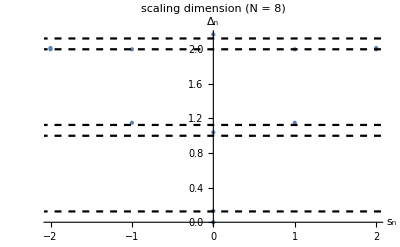
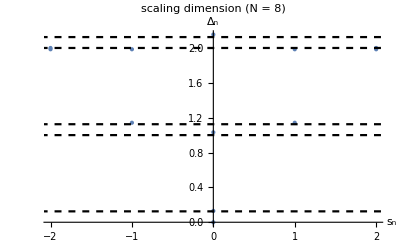

```mathematica
plotΔs[8]
```

momenta: {0,0,0,1.,-1.,2.,-2.,1.,-1.,2.,-2.,0}, found ñ = {6,10}

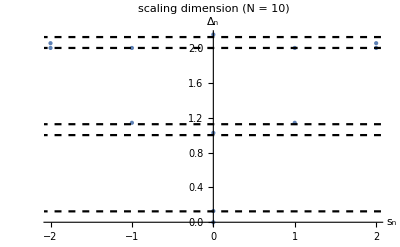
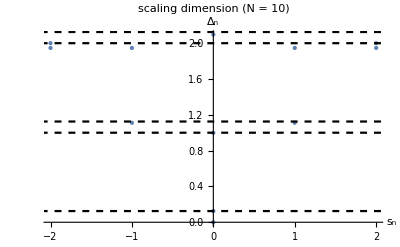
{16.09375,{-Graphics-,-Graphics-}}

```mathematica
plotΔs[10]//Timing
```

## A Tree Tensor Network

```mathematica
L0=12;
```

### Find groundstate

We find the groundstate energy and state :

```mathematica
Timing[(Hspins=Eigensystem[hamiltonianNconM[L0]//N//SparseArray,1,Method->"Arnoldi"])⟦1⟧]
state0=Hspins⟦2,1⟧;
```

{4.96875,{-15.3226}}

This we reshape back into the tensor structure of fig 1 a, and check that this indeed gives the right energy :

```mathematica
groundstate=ArrayReshape[state0,Table[2,{L0}]];
```

```mathematica
ncon[{groundstate,hamiltonianNcon[L0],groundstate*},{Range[L0]+L0,Range[2 L0],Range[L0]}]==state0*.hamiltonianNconM[L0].state0
```

True

### Compute reduced density matrix

```mathematica
legsψc=(-Range[L0/2])~Join~Range[L0/2]
legsψ=(-Range[L0/2]-L0/2)~Join~Range[L0/2]
```

{-1,-2,-3,-4,-5,-6,1,2,3,4,5,6}

{-7,-8,-9,-10,-11,-12,1,2,3,4,5,6}

```mathematica
ρred=ncon[{groundstate,groundstate*},{legsψ,legsψc}];
```

### Find vectors with highest occupancy in groundstate

```mathematica
χ=8;
```

```mathematica
makematrix[operator_]:=ArrayReshape[operator,{#,#}&[√Length[Flatten[operator]]]]
```

```mathematica
(eigensystemρ=Eigensystem[makematrix[ρred],χ,Method->"Arnoldi"])⟦1⟧
```

{0.723257,0.248372,0.0203185,0.00697754,0.00076536,0.000262831,0.0000215013,0.0000123213}

```mathematica
Ws=ArrayReshape[#,Table[2,{L0/2}]]&/@eigensystemρ⟦2⟧;
```

### Compute effective field and interaction for Ws

This implements the diagrams to compute J and I. (the legs statement is a bit of a trick, but of course it can also be found by hand)

```mathematica
(Subscript[J, 1]=ncon[{Ws,hamiltonianNcon[L0/2,periodic->False],Ws*},{{-1}~Join~Range[L0/2],Range[L0],{-2}~Join~(Range[L0/2]+L0/2)}])//Dimensions
legs=addop[Table[{-{1,3,2,4}⟦i⟧}~Join~(Range[L0/2]+Quotient[i,3] L0/2 ),{i,4}],{4,5}]
(Subscript[i, 1]=ncon[{Ws,Ws*,Ws,Ws*,isinginteraction},legs])//Dimensions
```

{8,8}

{{-1,1,2,3,4,5,6},{-3,1,2,3,13,14,6},{-2,7,8,9,10,11,12},{-4,7,8,9,10,11,12},{4,5,13,14}}

taking trace

taking trace

{8,8,8,8}

### Subsequent steps

First we try by hand:

```mathematica
Q=2;
Lnew=4;
```

```mathematica
(Subscript[H, Q]=hamiltonianNconM[Lnew,field->Subscript[J, Q-1],interaction->Subscript[i, Q-1]]//N//SparseArray)//Dimensions//Timing
(Subscript[ψ0, Q]=ArrayReshape[Eigensystem[Subscript[H, Q],1,Method->"Arnoldi"]⟦2,1⟧,Table[χ,{Lnew}]])//Dimensions//Timing
```

{1.04688,{4096,4096}}

{0.07813,{8,8,8,8}}

```mathematica
{(-Range[Lnew/2])~Join~Range[Lnew/2],(-Range[Lnew/2]-Lnew/2)~Join~Range[Lnew/2]}
```

{{-1,-2,1,2},{-3,-4,1,2}}

```mathematica
(Subscript[ρ, Q]=ncon[{Subscript[ψ0, Q],Subscript[ψ0, Q]*},{{-1,-2,1,2},{-3,-4,1,2}}])//Dimensions//Timing
```

{0.,{8,8,8,8}}

```mathematica
(Subscript[W, Q]=ArrayReshape[#,Table[d,{Lnew/2}]]&/@Eigensystem[makematrix[Subscript[ρ, Q]],χ,Method->"Arnoldi"]⟦2⟧)//Dimensions//Timing
```

{0.,{8,8,8}}

```mathematica
(Subscript[J, Q]=ncon[{Subscript[W, Q],hamiltonianNcon[Lnew/2,interaction->Subscript[i, Q-1],field->Subscript[J, Q-1],periodic->False],Subscript[W, Q]*},{{-1}~Join~Range[Lnew/2],Range[Lnew],{-2}~Join~(Range[Lnew/2]+Lnew/2)}])//Dimensions
legs=addop[Table[{-{1,3,2,4}⟦i⟧}~Join~(Range[Lnew/2]+Quotient[i,3] Lnew/2 ),{i,4}],{4,5}]
(Subscript[i, Q]=ncon[{Subscript[W, Q],Subscript[W, Q]*,Subscript[W, Q],Subscript[W, Q]*,Subscript[i, Q-1]},legs])//Dimensions
```

{8,8}

{{-1,1,2},{-3,1,2},{-2,3,4},{-4,3,6},{4,5,5,6}}

taking trace

{8,8,8,8}

## Make TTN

We now notice the regularity and combine the previous steps in one module :

```mathematica
Options[makeTTN]={periodic->True,interaction-> isinginteraction,field->isingfield };
makematrix[operator_]:=ArrayReshape[operator,{#,#}&[√Length[Flatten[operator]]]];
prtrace=False;
makeTTN[L0_,Ln_,χ_,Qmax_,OptionsPattern[]]:=Module[{Lnow,χnow},
{Lnow,χnow}={L0,Dimensions[OptionValue[field]]⟦1⟧};
Subscript[J, 0]=OptionValue[field];
Subscript[i, 0]=OptionValue[interaction];
Monitor[Do[
Subscript[H, Q]=hamiltonianNconM[Lnow,interaction->Subscript[i, Q-1],field->Subscript[J, Q-1]]//N//SparseArray;
Subscript[ψ0, Q]=ArrayReshape[Eigensystem[Subscript[H, Q],1,Method->"Arnoldi"]⟦2,1⟧,Table[χnow,{Lnow}]];
Subscript[ρ, Q]=ncon[{Subscript[ψ0, Q],Subscript[ψ0, Q]*},{(-Range[Lnow/2])~Join~Range[Lnow/2],(-Range[Lnow/2]-Lnow/2)~Join~Range[Lnow/2]}];
Subscript[W, Q]=ArrayReshape[#,Table[χnow,{Lnow/2}]]&/@Eigensystem[makematrix[Subscript[ρ, Q]],χ,Method->"Arnoldi"]⟦2⟧;
Subscript[J, Q]=ncon[{Subscript[W, Q],hamiltonianNcon[Lnow/2,interaction->Subscript[i, Q-1],field->Subscript[J, Q-1],periodic->False],Subscript[W, Q]*},{{-1}~Join~Range[Lnow/2],Range[Lnow],{-2}~Join~(Range[Lnow/2]+Lnow/2)}];
legs=addop[Table[{-{1,3,2,4}⟦i⟧}~Join~(Range[Lnow/2]+Quotient[i,3] Lnow/2 ),{i,4}],{Lnow/2,Lnow/2+1}];
Subscript[i, Q]=ncon[{Subscript[W, Q],Subscript[W, Q]*,Subscript[W, Q],Subscript[W, Q]*,Subscript[i, Q-1]},legs];
{Lnow,χnow}={Ln,χ};
,{Q,Qmax}],Q];
Print["Constructed TTN for a spin chain of length ",6 2^Qmax," with χ = ",χ,". First 10 lowest energies: ",Eigenvalues[hamiltonianNconM[2,interaction->Subscript[i, Qmax],field->Subscript[J, Qmax]],10,Method->"Arnoldi"]];
Print["Ising exact value: ",6 2^Qmax analyticf[1.0,6 2^Qmax]/.model->"Ising"];
]
```

```mathematica
Timing[makeTTN[12,4,8,3]]⟦1⟧
```

Constructed TTN for a spin chain of length 48 with χ = 8. First 10 lowest energies: {-61.1156,-61.0682,-60.6491,-60.6088,-60.5926,-60.1411,-60.1355,-60.0535,-59.9345,-59.7887}

Ising exact value: -61.1264

7.45313

```mathematica
Timing[makeTTN[12,4,8,5]]⟦1⟧
```

Constructed TTN for a spin chain of length 192 with χ = 8. First 10 lowest energies: {-244.381,-244.347,-244.09,-244.069,-244.022,-243.726,-243.723,-243.693,-243.597,-243.409}

Ising exact value: -244.465

9.703125